Ultima atualização: 14/04/21 - 17h

## Load Radia

```mathematica
ClearAll["Global`*"]
```

```mathematica
<<Radia`;
RadPlot3DOptions[];
radUtiDelAll[]; (*Erase all previous elements*)
```

Radia Version: 4.31 is loaded

Radia is copyright ESRF, France.

Portions copyright Synchrotron SOLEIL, France.

Portions copyright Wolfram Research, Inc.

## Functions

### BlockGeometry

```mathematica
idBlockGeometry[checkgeo_]:=(
Module[{geo1,geo2,geo3},

(*Geo A1, Delta 52.5*)
If[checkgeo==1,
geo1={{-21.5,-50},{21.5,-50},{22.5,-49},{22.5,-41.8},{16.794,-37.654},{-16.794,-37.654},{-22.5,-41.8},{-22.5,-49}};
geo2={{16.794,-37.654},{16.794,-33.946},{-16.794,-33.946},{-16.794,-37.654}};
geo3={{16.794,-33.946},{22.5,-29.8},{22.5,-19.3},{5.25,0.0},{-5.25,0.0},{-22.5,-19.3},{-22.5,-29.8},{-16.794,-33.946}};
];

If[checkgeo==2,
geo1={{16.794,-37.654},{16.794,-33.946},{-16.794,-33.946},{-16.794,-37.654}};
geo2={{16.794,-33.946},{22.5,-29.8},{22.5,-19.3},{5.25,0.0},{-5.25,0.0},{-22.5,-19.3},{-22.5,-29.8},{-16.794,-33.946}};
];

Return[{geo1,geo2,geo3}]
];
)
```

### cassetteDraw

```mathematica
cassetteDraw::usage = "magnetizations = Lista das magnetizações dos blocos de um cassete (lista de tamanho n); blockGeo = {geo1,geo2,geo3}; 
termination = {{lista de magnetizacoes na entrada}, {lista de espessuras na entrada}, {lista de espaçamentos na entrada},{lista de magnetizacoes na saída}, {lista de espessuras na saída}, {lista de espaçamentos na saída}}"; 


idCassetteDraw[magnetizations_,blockGeo_,posErrors_,termination_,periodL_,blockThick_,gap_,blockGap_,subdiv_]:=(
Module[{cassette,block,obj,obj1,obj2,obj3,blocknumber,vacodym745ap,termLength,i,j,parts,randomErrorY,randomErrorZ,longPos},

cassette=radObjCnt[{}];
parts=Length[blockGeo];
obj=ConstantArray[{},parts];
blocknumber=Length[magnetizations]+Length[termination[[1]]]+Length[termination[[4]]];

(*Position Errors*)
If[posErrors[[1]]>0,
randomErrorY=Table[RandomVariate[NormalDistribution[posErrors[[1]]/2,(posErrors[[1]]/2)/3]],{i,1,blocknumber}]*RandomChoice[{-1,1},blocknumber];
,
randomErrorY=ConstantArray[0,blocknumber];
];
If[posErrors[[2]]>0,
randomErrorZ=Table[RandomVariate[NormalDistribution[posErrors[[2]]/2,(posErrors[[2]]/2)/3]],{i,1,blocknumber}]*RandomChoice[{-1,1},blocknumber];
,
randomErrorZ=ConstantArray[0,blocknumber];
];

(*===== Termination Front =====*)
block=ConstantArray[{},Length[termination[[1]]]];

For[i=1,i≤ Length[termination[[1]]],i++,
block[[i]]=radObjCnt[{}];

(*Next Block Position*)
If[i≤1,
longPos=0,
longPos=longPos+0.5*termination[[2,i-1]]+termination[[3,i-1]]+0.5*termination[[2,i]];
];

(*Create the Block Object*)
For[j=1,j≤ parts,j++,
(*Extrude part*)
obj[[j]]=radObjThckPgn[longPos,termination[[2,i]],blockGeo[[j]],termination[[1,i]]];
(*Part Subdivision*)
radObjDivMag[obj[[j]],subdiv[[j]]];
(*Add Part to block*)
radObjAddToCnt[block[[i]],{obj[[j]]}];
];

(*Position Error*)
radTrfOrnt[block[[i]],radTrfTrsl[{0,randomErrorY[[i]],randomErrorZ[[i]]}]];

(*Apply Material and Magnetization*)
vacodym745ap=radMatLin[{0.06,0.17},termination[[1,i]]];
radMatApl[block[[i]],vacodym745ap];

(*Add to Cassette*)
radObjAddToCnt[cassette,{block[[i]]}];
];

(*===== Periods =====*)
block=ConstantArray[{},Length[magnetizations]];

For[i=1,i≤ Length[magnetizations],i++,
block[[i]]=radObjCnt[{}];

(*Block Position*)
If[i≤1,
longPos=longPos+0.5*termination[[2,-1]]+termination[[3,-1]]+0.5*blockThick;
,
longPos=longPos+blockThick+blockGap;
];

For[j=1,j≤ parts,j++,
obj[[j]]=radObjThckPgn[longPos,blockThick,blockGeo[[j]],magnetizations[[i]]];
(*Part Subdivision*)
radObjDivMag[obj[[j]],subdiv[[j]]];
(*Add Part to block*)
radObjAddToCnt[block[[i]],{obj[[j]]}];
];

(*Position Error*)
radTrfOrnt[block[[i]],radTrfTrsl[{0,randomErrorY[[i]],randomErrorZ[[i]]}]];

(*Apply Material and Magnetization*)
vacodym745ap=radMatLin[{0.06,0.17},magnetizations[[i]]];
radMatApl[block[[i]],vacodym745ap]; 

(*Add to Cassette*)
radObjAddToCnt[cassette,{block[[i]]}];

];

(*===== Termination Back =====*)
block=ConstantArray[{},Length[termination[[1]]]];

For[i=1,i≤ Length[termination[[4]]],i++,
block[[i]]=radObjCnt[{}];

(*Next Block Position*)
If[i≤ 1,
longPos=longPos+blockThick/2+termination[[6,1]]+termination[[5,1]]/2;
,
longPos=longPos+0.5*termination[[5,i-1]]+termination[[6,i]]+0.5*termination[[5,i]];
];

For[j=1,j≤ parts,j++,
obj[[j]]=radObjThckPgn[longPos,termination[[5,i]],blockGeo[[j]],termination[[4,i]]];
(*Part Subdivision*)
radObjDivMag[obj[[j]],subdiv[[j]]];
(*Add Part to block*)
radObjAddToCnt[block[[i]],{obj[[j]]}];
];

(*Position Error*)
radTrfOrnt[block[[i]],radTrfTrsl[{0,randomErrorY[[i]],randomErrorZ[[i]]}]];

(*Apply Material and Magnetization*)
vacodym745ap=radMatLin[{0.06,0.17},termination[[4,i]]];
radMatApl[block[[i]],vacodym745ap]; 

(*Add to Cassette*)
radObjAddToCnt[cassette,{block[[i]]}];

];

Return[cassette]
];
)
```

### IDDraw

```mathematica
idDraw[typeID_,gap_,nPeriods_,periodL_,blockGeo_,blockThick_,blockGap_,magnetizations_,terminations_,mode_,subdiv_ ,posErrors_ :{0,0},gap2_ :0]:=(
Module[{device,cassette,mag,cassetteD,modeslist,phase,i,displacement,cassPos},
device=radObjCnt[{}];
cassette=ConstantArray[{},4];

(*==== Generate Cassettes =====*)
For[i=1,i≤Length[magnetizations],i++,
cassette[[i]]=idCassetteDraw[magnetizations[[i]],blockGeo,posErrors,terminations[[i]],periodL,blockThick,gap,blockGap,subdiv];

(*Apply Gap*)
radTrfOrnt[cassette[[i]],radTrfTrsl[{0,0,-gap/2}]];

If[typeID=="DeltaUndulator",
(*Apply Phase*)
(*modeslist={{0,0,0,0},{-1/4,0,-1/4,0},{-1/2,0,-1/2,0},{-1/4,0,1/4,0},{-1/4,-1/4,0,0},{-1/4,0,0,-1/4}}*periodL;*)
modeslist={{0,0,0,0},{1/4,0,1/4,0},{1/2,0,1/2,0},{1/4,0,-1/4,0},{-1/4,-1/4,0,0},{-1/4,0,0,-1/4}}*periodL;
phase=modeslist[[mode]];
radTrfOrnt[cassette[[i]],radTrfTrsl[{phase[[i]],0,0}]];

(*Apply Rotation*)
radTrfOrnt[cassette[[i]],radTrfRot[{0,0,0},{1,0,0},(i-1)*Pi/2]];
];

If[typeID=="PlanarUndulator",
(*Apply Phase*)
modeslist={{0,0},{0,-1/2},{0,-1/4},{0,1/2},{0,1/4}}*periodL;
phase=modeslist[[mode]];
radTrfOrnt[cassette[[i]],radTrfTrsl[{phase[[i]],0,0}]];

(*Apply Rotation*)
radTrfOrnt[cassette[[i]],radTrfRot[{0,0,0},{1,0,0},(i-1)*Pi]];
];

If[typeID=="EPU",
(*Apply Phase*)
modeslist={{0,0,0,0},{-1/4,0,-1/4,0},{-1/2,0,-1/2,0},{-1/4,0,1/4,0}}*periodL;
phase=modeslist[[mode]];
radTrfOrnt[cassette[[i]],radTrfTrsl[{phase[[i]],0,0}]];

(*Apply Position*)
zdesloc=gap+50/2; ydesloc=gap2+22; a=Min[Flatten[blockGeo,1][[All,2]]];
cassPos={{0,-ydesloc,0},{0,ydesloc,0},{0,ydesloc,2*zdesloc},{0,-ydesloc,2*zdesloc}};

radTrfOrnt[cassette[[i]],radTrfTrsl[cassPos[[i]]]];
];


radObjAddToCnt[device,{cassette[[i]]}];
];

If[typeID=="DeltaUndulator",
(*Rotate ID*)
radTrfOrnt[device,radTrfRot[{0,0,0},{1,0,0},-Pi/4]];
];

(*Adjust Axis*)
radTrfOrnt[device,radTrfRot[{0,0,0},{0,1,0},-Pi/2]];
radTrfOrnt[device,radTrfRot[{0,0,0},{0,0,1},Pi/2]];

Return[device];
];
)
```

### Generate Block Mag

```mathematica
idGenerateMag[typeID_,nPeriods_,periodL_,blockThick_,blockGap_,symmetry_,magnAmp_,magError_ :0,magAmpError_ :0.02,magTheta_ :1]:=(
Module[{mag,magnetization,j,i,termination,phi,theta,dmag},

(*===== ID Type =====*)
If[typeID=="DeltaUndulator",
mag={{{magnAmp,0,0},{0,0,magnAmp},{-magnAmp,0,0},{0,0,-magnAmp}},{{magnAmp,0,0},{0,0,magnAmp},{-magnAmp,0,0},{0,0,-magnAmp}},{{-magnAmp,0,0},{0,0,-magnAmp},{magnAmp,0,0},{0,0,magnAmp}},{{-magnAmp,0,0},{0,0,-magnAmp},{magnAmp,0,0},{0,0,magnAmp}}};
];

If[typeID=="PlanarUndulator",
mag={{{magnAmp,0,0},{0,0,magnAmp},{-magnAmp,0,0},{0,0,-magnAmp}},{{-magnAmp,0,0},{0,0,-magnAmp},{magnAmp,0,0},{0,0,magnAmp}}};
];

If[typeID=="EPU",
mag={{{-magnAmp,0,0},{0,0,-magnAmp},{magnAmp,0,0},{0,0,magnAmp}},{{-magnAmp,0,0},{0,0,-magnAmp},{magnAmp,0,0},{0,0,magnAmp}},{{magnAmp,0,0},{0,0,-magnAmp},{-magnAmp,0,0},{0,0,magnAmp}},{{magnAmp,0,0},{0,0,-magnAmp},{-magnAmp,0,0},{0,0,magnAmp}}};
];

(*===== Create Cassette Magnetizations =====*)
magnetization=ConstantArray[{},Length[mag]];

For[j=1,j≤ Length[mag],j++,
magnetization[[j]]=Nest[Join[mag[[j]],#,1]&,mag[[j]],(nPeriods-1)];
If[symmetry=="symmetric",
magnetization[[j]]=Delete[magnetization[[j]],-1];
,
magnetization[[j]]=Join[magnetization[[j]],{magnetization[[j,1]]}];
];
];

(*===== Generate Errors =====*)
phi=RandomReal[{0,2*Pi},Length[Flatten[magnetization,1]]];
phi=ArrayReshape[phi,{Length[magnetization],Length[magnetization[[1]]]}];

theta=Table[RandomVariate[NormalDistribution[0,(magTheta*Pi/180)/3]],{i,1,Length[Flatten[magnetization,1]]}];
theta=ArrayReshape[theta,{Length[magnetization],Length[magnetization[[1]]]}]; 

If[magError≥1,
dmag=1+Table[RandomVariate[NormalDistribution[0,magAmpError/3]],{i,1,Length[Flatten[magnetization,1]]}];
dmag=ArrayReshape[dmag,{Length[magnetization],Length[magnetization[[1]]]}]; 
,
dmag=ConstantArray[1,{Length[magnetization],Length[magnetization[[1]]]}];
phi=phi*0;
theta=theta*0;
];

(*===== Apply Errors =====*)
For[i=1,i≤ Length[magnetization],i++,
magnetization[[i]]=magnetization[[i]]*dmag[[i]];

For[j=1,j≤ Length[magnetization[[1]]],j++,
If[Mod[j,2]≤0,
magnetization[[i,j]]=RotationMatrix[phi[[i,j]],{0,0,1}].RotationMatrix[theta[[i,j]],{0,1,0}].magnetization[[i,j]];
,
magnetization[[i,j]]=RotationMatrix[phi[[i,j]],{1,0,0}].RotationMatrix[theta[[i,j]],{0,1,0}].magnetization[[i,j]];
];
]

];
Return[magnetization]
];
)
```

### GenerateTermination Mag

```mathematica
idGenerateTerm[termType_,blockThick_,blockGap_,periodL_,magnAmp_,magFront_ :{{}},magBack_ :{{}},magError_ :0,magAmpError_ :0.02,magTheta_ :1]:=(
Module[{termination,termMagFront,termMagBack,termBlockThick,termBlockGap,dmag,phi,theta,size},
(*----- ThreeBlocksAntiSym Termination -----*)
If[termType=="ThreeBlocksAntiSym",
If[Length[magFront[[1]]]≥ 3,
termMagFront=magFront;
,
termMagFront={{{0,0,magnAmp},{-magnAmp,0,0},{0,0,-magnAmp}},{{0,0,magnAmp},{-magnAmp,0,0},{0,0,-magnAmp}},{{0,0,-magnAmp},{magnAmp,0,0},{0,0,magnAmp}},{{0,0,-magnAmp},{magnAmp,0,0},{0,0,magnAmp}}};
];

If[Length[magBack[[1]]]≥ 3,
termMagBack=magBack;
,
termMagBack={{{0,0,magnAmp},{-magnAmp,0,0},{0,0,-magnAmp}},{{0,0,magnAmp},{-magnAmp,0,0},{0,0,-magnAmp}},{{0,0,-magnAmp},{magnAmp,0,0},{0,0,magnAmp}},{{0,0,-magnAmp},{magnAmp,0,0},{0,0,magnAmp}}};
];

termBlockThick={1/4,1/2,3/4}*blockThick;
termBlockGap={0.875*periodL/4-((0.25+0.5)/2*blockThick),0.875*periodL/4-((0.5+0.75)/2*blockThick),0.875*periodL/4-((0.75+1)/2*blockThick)};

termination=Table[{termMagFront[[i]],termBlockThick,termBlockGap,termMagBack[[i]],Reverse[termBlockThick],Reverse[termBlockGap]},{i,1,Length[termMagFront]}];
];
(*-------------------------------------------------------------*)
(*----- FourBlocksAntiSym Termination -----*)
If[termType=="FourBlocksAntiSym",
If[Length[magFront[[1]]]≥ 4,
termMagFront=magFront;
,
termMagFront={{{magnAmp,0,0},{0,0,magnAmp},{-magnAmp,0,0},{0,0,-magnAmp}},{{magnAmp,0,0},{0,0,magnAmp},{-magnAmp,0,0},{0,0,-magnAmp}},{{-magnAmp,0,0},{0,0,-magnAmp},{magnAmp,0,0},{0,0,magnAmp}},{{-magnAmp,0,0},{0,0,-magnAmp},{magnAmp,0,0},{0,0,magnAmp}}};

(*Apply Errors*)
If[magError≥1,
size=Dimensions[termMagFront];
dmag=1+Table[RandomVariate[NormalDistribution[0,magAmpError/3]],{i,1,Length[Flatten[termMagFront,1]]}];
termMagFront=Flatten[termMagFront,1]*dmag;

phi=RandomReal[{0,2*Pi},Length[termMagFront]];
theta=Table[RandomVariate[NormalDistribution[0,(magTheta*Pi/180)/3]],{i,1,Length[termMagFront]}];

For[i=1,i≤ Length[termMagFront],i++,
If[Mod[i,2]≤0,
termMagFront[[i]]=RotationMatrix[phi[[i]],{0,0,1}].RotationMatrix[theta[[i]],{0,1,0}].termMagFront[[i]];
,
termMagFront[[i]]=RotationMatrix[phi[[i]],{1,0,0}].RotationMatrix[theta[[i]],{0,1,0}].termMagFront[[i]];
]];
termMagFront=ArrayReshape[termMagFront,size];
]
];

If[Length[magBack[[1]]]≥ 4,
termMagBack=magBack;
,
termMagBack={{{0,0,magnAmp},{-magnAmp,0,0},{0,0,-magnAmp},{magnAmp,0,0}},{{0,0,magnAmp},{-magnAmp,0,0},{0,0,-magnAmp},{magnAmp,0,0}},{{0,0,-magnAmp},{magnAmp,0,0},{0,0,magnAmp},{-magnAmp,0,0}},{{0,0,-magnAmp},{magnAmp,0,0},{0,0,magnAmp},{-magnAmp,0,0}}};

(*Apply Errors*)
If[magError≥1,
size=Dimensions[termMagBack];
dmag=1+Table[RandomVariate[NormalDistribution[0,magAmpError/3]],{i,1,Length[Flatten[termMagBack,1]]}];
termMagBack=Flatten[termMagBack,1]*dmag;

phi=RandomReal[{0,2*Pi},Length[termMagBack]];
theta=Table[RandomVariate[NormalDistribution[0,(magTheta*Pi/180)/3]],{i,1,Length[termMagBack]}];

For[i=1,i≤ Length[termMagBack],i++,
If[Mod[i,2]>0,
termMagBack[[i]]=RotationMatrix[phi[[i]],{0,0,1}].RotationMatrix[theta[[i]],{0,1,0}].termMagBack[[i]];
,
termMagBack[[i]]=RotationMatrix[phi[[i]],{1,0,0}].RotationMatrix[theta[[i]],{0,1,0}].termMagBack[[i]];
]];
termMagBack=ArrayReshape[termMagBack,size];
]
];

termBlockThick={3.25,3.25,9.75,9.75};
termBlockGap={8.7,2.0,3.3,1.0};

termination=Table[{termMagFront[[i]],termBlockThick,termBlockGap,termMagBack[[i]],Reverse[termBlockThick],Reverse[termBlockGap]},{i,1,Length[termMagFront]}];
];
(*-------------------------------------------------------------*)

Return[termination]
];
)
```

### Solve

```mathematica
idSolve[device_,randomization_ :{1*^-10,1*^-10,1*^-10}]:=(
Module[{abs,rel,zero,re,t0,t1},
t0=AbsoluteTime[];

radFldLenTol[randomization[[1]],randomization[[2]],randomization[[3]]];

re=RadSolve[device,1*^-10,100000];
(*t1=AbsoluteTime[];
Print["> Insertion Device solved: (Elapsed Time: ",t1-t0,"[s])"]*)
]
)
```

### Field Calc

```mathematica
idField[undulator_,li_,lf_,lNpts_,{posV_,posH_},display_,oneplot_]:=(
Module[{lstep,t0,t1,baxis,btotal,axispoints,plot},
lstep=(lf-li)/lNpts;
t0=AbsoluteTime[];

(*----- Axis Field Calc -----*)
baxis=Table[radFld[undulator,"b",{posH,posV,z}],{z,li,lf-lstep,lstep}];

t1=AbsoluteTime[];
(*Print["> Field Components: (elapsed time: ",t1-t0 ,"[s])"];*)

(*----- Plots -----*)
If[display≥ 1,
plot=ConstantArray[{},3];
(*Axis Plot*)
axispoints=Table[li+(n-1)*lstep,{n,1,lNpts}];
plot[[1]]=ListLinePlot[Table[{axispoints[[i]],baxis[[i,1]]},{i,1,lNpts}],Frame->True,FrameLabel->{Style["Z [mm]",12],Style["Magnetic Field [T]",12]},PlotTheme->"Detailed",ImageSize->Medium,PlotRange->All,PlotLegends->Placed[{"Bx"},Above]];
plot[[2]]=ListLinePlot[Table[{axispoints[[i]],baxis[[i,2]]},{i,1,lNpts}],Frame->True,FrameLabel->{Style["Z [mm]",12],Style["Magnetic Field [T]",12]},PlotTheme->"Detailed",PlotStyle->{Orange},ImageSize->Medium,PlotRange->All,PlotLegends->Placed[{"By"},Above]];
plot[[3]]=ListLinePlot[Table[{axispoints[[i]],baxis[[i,3]]},{i,1,lNpts}],Frame->True,FrameLabel->{Style["Z [mm]",12],Style["Magnetic Field [T]",12]},PlotTheme->"Detailed",PlotStyle->{Green},ImageSize->Medium,PlotRange->All,PlotLegends->Placed[{"Bz"},Above]];

If[oneplot≥1,
maxims=Table[{i,Max[baxis[[All,i]]]},{i,1,3}];
plotOrder=SortBy[maxims,Last];
Print[Show[Table[plot[[plotOrder[[-i,1]]]],{i,1,3}]]];
,
Print[GraphicsRow[{plot[[1]],plot[[2]],plot[[3]]},Spacings->{0,10},ImageSize->{1200,300},AspectRatio->Full]];
];
];

Return[baxis]
];
)
```

### Field Integral

```mathematica
idFieldInt[undulator_,li_,lf_,lstep_,baxis_,display_,oneplot_]:=(
Module[{i,dz,area,area2,integral,integral2,firstInt,secondInt,axispoints,plot,t0,t1},
(*----- First Integral -----*)
t0=AbsoluteTime[];
dz=lstep;

area=Table[{(baxis[[i,1]]+baxis[[i+1,1]])/2*dz,(baxis[[i,2]]+baxis[[i+1,2]])/2*dz,(baxis[[i,3]]+baxis[[i+1,3]])/2*dz},{i,1,Length[baxis]-1}];
integral=Accumulate[area]; (*T.mm*)
firstInt=integral*10^4/10 ;(*G.cm*)

(*----- Second Integral -----*)
area2=Table[{(integral[[i,1]]+integral[[i+1,1]])/2*dz,(integral[[i,2]]+integral[[i+1,2]])/2*dz,(integral[[i,3]]+integral[[i+1,3]])/2*dz},{i,1,Length[integral]-1}];
integral2=Accumulate[area2];(*T.mm.b2*)
secondInt=(integral2*10^4/100)/1000; (*kG.cm.b2*)

t1=AbsoluteTime[];

(*Print["> Field Integrals: elapsed time = ",(t1-t0)," [s]"];*)

(*Print["First integrals : ", firstInt[[-1]]," [G.cm]"];
Print["Second integrals : ", secondInt[[-1]]," [kG.cm.b2]"];*)

(*----- Plots -----*)
If[display≥ 1,
plot=ConstantArray[{},3];
axispoints=Table[(li+lstep/2)+(n-1)*lstep,{n,1,Length[baxis]-1}];

plot[[1]]=ListLinePlot[Table[{axispoints[[i]],firstInt[[i,1]]},{i,1,Length[firstInt]}],Frame->True,FrameLabel->{Style["Z [mm]",12],Style["Field Integral [G.cm]",12]},PlotTheme->"Detailed",ImageSize->Medium,PlotLegends->Placed[{"Bx"},Above]];
plot[[2]]=ListLinePlot[Table[{axispoints[[i]],firstInt[[i,2]]},{i,1,Length[firstInt]}],Frame->True,FrameLabel->{Style["Z [mm]",12],Style["Field integral [G.cm]",12]},PlotTheme->"Detailed",PlotStyle->{Orange},ImageSize->Medium,PlotLegends->Placed[{"By"},Above]];
plot[[3]]=ListLinePlot[Table[{axispoints[[i]],firstInt[[i,3]]},{i,1,Length[firstInt]}],Frame->True,FrameLabel->{Style["Z [mm]",12],Style["Field integral [G.cm]",12]},PlotTheme->"Detailed",PlotStyle->{Green},ImageSize->Medium,PlotLegends->Placed[{"Bz"},Above]];

If[oneplot≥1,
maxims=Table[{i,Max[firstInt[[All,i]]]},{i,1,3}];
plotOrder=SortBy[maxims,Last];
Print[Show[Table[plot[[plotOrder[[-i,1]]]],{i,1,3}]]];
,
Print[GraphicsRow[plot,Spacings->{0,10},ImageSize->{1200,300},AspectRatio->Full]];
];
];

Return[{firstInt,secondInt}]
];
)
```

### Trajectory - RungeKutta4

```mathematica
idTrajectory::usage = "IDRungeKuttaTrajectory[device, energy, r0, smax, rkstep]: Calculates the particle trajectory using the Runge-Kutta algorithm. The particle energy must be in GeV, r0 is the initial position and normalized momentum vector {x0, y0, z0, dx0ds, dy0ds, dz0ds}, smax and rkstep are the final longitudinal position and the Runge-Kutta step. All positions are in millimeters.";

idTrajectory[device_, energy_,r0_,smax_,rkstep_,display_] := Module[
{trajectory, ElectronRestEnergy, LightSpeed, beta, brho, a, b, b1, b2, b3, r,rp, r1, r2, r3, drds1, drds2, drds3, drds4, i, sm, step, t0, t1,p1,p2},

t0=AbsoluteTime[];

ElectronRestEnergy=510998.92811; (*[eV]*)
LightSpeed=299792458;(*[m/s]*)

beta=Sqrt[1.0-(1.0/((energy*1000000000/ElectronRestEnergy)^2))];
brho=(beta*energy*1000000000/LightSpeed);
a=1.0/brho;

r1 = {0,0,0,0,0,0};
r2 = {0,0,0,0,0,0};
r3 = {0,0,0,0,0,0};
r= r0;

(*from mm to m*)
r[[1]]= r[[1]]/1000; r[[2]]= r[[2]]/1000; r[[3]]= r[[3]]/1000;
sm = smax/1000;
step = rkstep/1000;

trajectory={};
AppendTo[trajectory, {r[[1]]*1000, r[[2]]*1000, r[[3]]*1000, r[[4]], r[[5]], r[[6]]}];

While [r[[3]]<sm,
rp =r;
b=radFld[device, "BxByBz", 1000*rp[[;;3]]];
	drds1=auxIDNewtonLorentzEquation[a,r,b];
r1=rp+(step/2.0)*drds1;

b1=radFld[device, "BxByBz", 1000*r1[[;;3]]];
	drds2=auxIDNewtonLorentzEquation[a,r1,b1];
r2=rp+(step/2.0)*drds2;

b2=radFld[device, "BxByBz", 1000*r2[[;;3]]];
drds3=auxIDNewtonLorentzEquation[a,r2,b2];
r3=rp+step*drds3;

b3=radFld[device, "BxByBz", 1000*r3[[;;3]]];
drds4=auxIDNewtonLorentzEquation[a,r3,b3];
r=rp+(step/6.0)*(drds1+2.0*drds2+2.0*drds3+drds4);

AppendTo[trajectory, {r[[1]]*1000, r[[2]]*1000, r[[3]]*1000, r[[4]], r[[5]], r[[6]]}];
];

t1=AbsoluteTime[];
(*Print["> IDRungeKuttaTrajectory: elapsed time = ",(t1-t0)," s"];*)

If[display≥ 1,
(*Plots*)
p1=ListLinePlot[Table[{trajectory[[i,3]],trajectory[[i,1]]},{i,1,Length[trajectory]}],Frame->True,FrameLabel->{Style["Z [mm]",12],Style["X [mm]",12]},PlotLabel->Style["X Direction Trajectory",Bold,12],PlotTheme->"Detailed",ImageSize->Medium];
p2=ListLinePlot[Table[{trajectory[[i,3]],trajectory[[i,2]]},{i,1,Length[trajectory]}],Frame->True,FrameLabel->{Style["Z [mm]",12],Style["Y [mm]",12]},PlotLabel->Style["Y Direction Trajectory",Bold,12],PlotTheme->"Detailed",ImageSize->Medium];

Print[Row[{p1,p2},"\t\t"]];
];

Return[trajectory];
];
```

### AuxRungeKutta

```mathematica
auxIDNewtonLorentzEquation[a_,r_,b_]:=Module[
{drds},
drds = {0,0,0,0,0,0};
drds[[1]]=r[[4]];
drds[[2]]=r[[5]];
drds[[3]]=r[[6]];
drds[[4]]=-a*(r[[5]]*b[[3]]-r[[6]]*b[[2]]);
drds[[5]]=-a*(r[[6]]*b[[1]]-r[[4]]*b[[3]]);
drds[[6]]=-a*(r[[4]]*b[[2]]-r[[5]]*b[[1]]);
Return[drds];
];
```

### PhaseError - RungeKutta

```mathematica
idPhaseError[baxis_,xo_,xf_,nx_,Trajetoria_,eEnergy_]:=(
Module[{eletron,mo,eRestEnergy,bfield,bfieldT,longAxis,ampX,ampY,ampZ,ampT,peakX,peakY,peakZ,peakT,longPeak,longPeakX,longPeakY,longPeakZ,longPeakT,periods,nperiods,periodL,kparam,gamma,lambda,intField0,intField,drop,phaseError,phase,j,jmin,rmsError,fitData,fitLin,linearFit,linearizedPhase,p3,a,b,I00,I0,p0,btotal,dx,c,s,errorP,t0,t1},
t0=AbsoluteTime[];

(*Check Inputs*)
If[Length[baxis≠ Length[Trajetoria]],Return["[ERROR] : Field vector and Trajectory Vector have not the same lenght."]];
If[eEnergy>100,Return["[ERROR] : Electron beam energy to high. Check if the input energy is in Gev."]];

(*Total Field*)
btotal=Sqrt[baxis[[All,1]]^2+baxis[[All,2]]^2+baxis[[All,3]]^2];

(*===== Parameters =====*)
eletron=1.60217662*^-19; mo=9.10938356*^-31;
eRestEnergy=510998.92811; (*[eV]*) (* == mo*c^2[J]*)
c=299792458; (*m/s*)

bfield=baxis;
bfieldT=btotal;

(*Principal Longitudinal Axis*)
dx=(xf-xo)/nx;
longAxis=Table[xo+(n-1)*dx,{n,1,nx}];

(* Longitudinal Axis from 0 *)
s=(longAxis-longAxis[[1]])/1000;  (*[m]*)

(*===== Find Peaks =====*)
ampT=0.1*Max[bfieldT];
ampX=ampY=ampZ=ampT;
(*Find Peaks*)
peakX=FindPeaks[bfield[[All,1]],0 ,0, ampX];
peakY=FindPeaks[bfield[[All,2]],0 ,0, ampY];
peakZ=FindPeaks[bfield[[All,3]],0 ,0, ampZ];
peakT=FindPeaks[bfieldT,0 ,0 , ampT];

(*===== Remove extremities from Total Field =====*)
drop=4; (*how many peaks to drop each side*)
peakT=Drop[peakT,{1,drop}];peakT=Drop[peakT,{-drop,-1}]; (*Drop extremity peaks*)
longPeakT=Table[s[[peakT[[i,1]]]],{i,1,Length[peakT]}]; (*Crate longitudinal axis based on total field*)

(*===== Remove extremities from Field Components =====*)
drop=3; (*how many peaks to drop each side*)
(*Z axis*)
If[Length[peakZ]>2*drop,
peakZ=Drop[peakZ,{1,drop}];peakZ=Drop[peakZ,{-drop,-1}];
longPeakZ=Table[longAxis[[peakZ[[i,1]]]],{i,1,Length[peakZ]}];
,
peakZ=ConstantArray[10^-5,{1,2}];
];
(*Y axis*)
If[Length[peakY]>2*drop,
peakY=Drop[peakY,{1,drop}];peakY=Drop[peakY,{-drop,-1}];
longPeakY=Table[longAxis[[peakY[[i,1]]]],{i,1,Length[peakY]}];
,
peakY=ConstantArray[10^-5,{1,2}];
];
(*X axis*)
If[Length[peakX]>2*drop,
peakX=Drop[peakX,{1,drop}];peakX=Drop[peakX,{-drop,-1}];
longPeakX=Table[longAxis[[peakX[[i,1]]]],{i,1,Length[peakX]}];
,
peakX=ConstantArray[10^-5,{1,2}];
];

(*===== Find the Principal Field Axis =====*)
If[Mean[peakX[[All,2]]]>Mean[peakY[[All,2]]],
If[Mean[peakX[[All,2]]]>Mean[peakZ[[All,2]]],
longPeak=longPeakX;
,
longPeak=longPeakZ;
]
,
If[Mean[peakY[[All,2]]]>Mean[peakZ[[All,2]]],
longPeak=longPeakY;
,
longPeak=longPeakZ;
]
];

periods=Table[longPeak[[i+1]]-longPeak[[i]],{i,1,Length[longPeak]-1}];

(*========= Magnet design =========*)
nperiods=Length[periods];
periodL=Mean[periods]; (*mm*)
gamma=eEnergy*10^9/eRestEnergy;
kparam=0.0934*periodL*Mean[peakT[[All,2]]];  (*!!!!!!!!!!!!! Todas componentes ou só 1? *)
lambda=((Mean[periods]/1000)/(2*(gamma^2)))*(1 + (kparam^2)/2); (*m*)

(*========= Phase Function =========*)
jmin=peakT[[1,1]];
phase={};

I0=Table[(((Trajetoria[[i,4]]^2+Trajetoria[[i+1,4]]^2)/2)+((Trajetoria[[i,5]]^2+Trajetoria[[i+1,5]]^2)/2))*(s[[i+1]]-s[[i]]),{i,1,jmin}];
p0=Pi/lambda*(s[[jmin]]/gamma^2+Sum[I0[[i]],{i,1,Length[I0]}]);
AppendTo[phase,p0];

For[j=jmin+1,j≤(peakT[[Length[peakT],1]]-2),j++,

I00=(((Trajetoria[[j,4]]^2+Trajetoria[[j+1,4]]^2)/2)+((Trajetoria[[j,5]]^2+Trajetoria[[j+1,5]]^2)/2))*(s[[j+1]]-s[[j]]);
AppendTo[I0,I00];
p0=Pi/lambda*(s[[j]]/gamma^2+Sum[I0[[i]],{i,1,Length[I0]}]);

AppendTo[phase,p0];
];

(*========= Fitting ========= *)
fitData=Table[{s[[i]]+longPeakT[[1]],phase[[i]]},{i,1,Length[phase]}];
fitLin=NonlinearModelFit[fitData,a*x+b,{a,b},x];

linearFit=Table[{s[[i]]+longPeakT[[1]],fitLin[s[[i]]+longPeakT[[1]]]},{i,1,Length[phase]}];
linearizedPhase=phase-linearFit[[All,2]];

p3=ListLinePlot[linearizedPhase*180/Pi,PlotLabel->"Linearized Phase",ImageSize->{300,200},Frame->True,FrameLabel->{" ","[deg]"}];

errorP=Table[Mean[linearizedPhase[[peakT[[i,1]]-peakT[[1,1]]+1;;peakT[[i+1,1]]-peakT[[1,1]]-1]]],{i,1,Length[peakT]-1}]*180/Pi;

t1=AbsoluteTime[];
(*Print["> Phase solved: elapsed time = ",t1-t0,"[s]"];*)

Return[errorP]
];
)
```

### BlocksPosition

```mathematica
idBlocksPosition[magnetizations_,terminations_,blockThick_,blockGap_]:=(
Module[{longPos,nTotalBl,nCasseteBl,blockidx},

nTotalBl=(Length[magnetizations[[1]]]+Length[terminations[[1,1]]]+Length[terminations[[1,4]]])*4;
nCasseteBl=nTotalBl/4;

longPos=ConstantArray[0,nCasseteBl]; 
blockidx=1;

For[i=2,i≤ Length[terminations[[1,1]]],i++,
longPos[[i]]=longPos[[i-1]]+0.5*terminations[[1,2,i-1]]+terminations[[1,3,i-1]]+0.5*terminations[[1,2,i]];
blockidx+=1;
];

	blockidx+=1;longPos[[blockidx]]=longPos[[blockidx-1]]+0.5*terminations[[1,2,-1]]+terminations[[1,3,-1]]+0.5*blockThick;

	For[i=2,i≤ Length[magnetizations[[1]]],i++,
blockidx+=1;
longPos[[blockidx]]=longPos[[blockidx-1]]+blockThick+blockGap;
];

	blockidx+=1;
longPos[[blockidx]]=longPos[[blockidx-1]]+blockThick/2+terminations[[1,6,1]]+terminations[[1,5,1]]/2;

For[i=2,i≤ Length[terminations[[1,4]]],i++,
blockidx+=1;
longPos[[blockidx]]=longPos[[blockidx-1]]+0.5*terminations[[1,5,i-1]]+terminations[[1,6,i]]+0.5*terminations[[1,5,i]];
];

Return[longPos]
];
)
```

## Calculation

### > Parameters

```mathematica
(*===== Magnetic Design =====*)
periodL=52.5; (*Period Length [mm]*)
gap=13.6; (*Minimum ID gap [mm]*)
nPeriods=21; (*number of periods without terminations*)
blockGap=0.125; (*space between blocks [mm]*)
eEnergy = 3; (*Particle energy [GeV]*)

(*==== Magnetic Blocks =====*)
blockGeo=idBlockGeometry[1]; (*Blocks Geometry: 1=A1*)
blockThick=13; (*Block Thickness [mm]*)
magInput=2; (*Type of input for Magnetizations: [1]Import from File ; [2]Aleatory Generation*)

fileNameB="Magnetizations.xlsx"; (*Magnetizations File name (with extension)*)
headLineB=0; (*Number of Head Lines on the File*)
fileNameT="Magnetizations_Term.xlsx"; (*Magnetizations File name (with extension)*)
headLineT=0; (*Number of Head Lines on the File*)

magnAmp=1.37; (*Remanent Block Magnetization [T]*)
magError=1; (*Include(1) or not(0) magnetization errors*)
magAmpError=0.02*magnAmp; (*Magnetization Amplitude Error [T]*)
magTheta=1; (*Magnetization Angle Error [deg]*)
posErrors={0,0}; (*Position Error Limit {x,y}+-[mm] *)

(*===== Other Parameters =====*)
mode=1; (*Phase: 1=Linear Hor. | 2=?*)
symmetry="antisymmetric"; (*ID symmetry: "symmetric" or "antisymmetric"*)
termType="FourBlocksAntiSym"; (*Termination Type: "FourBlocksAntiSym" | "ThreeBlocksAntiSym" | "ThreeBlocksAntiSymReal" | "ThreeBlockSym" | ?"Simple-Half"? *)
typeID="DeltaUndulator"; (*"DeltaUndulator" | "PlanarUndulator" | "EPU"*)
gap2=0; (*Horizontal gap in case of EPU undulator [mm]*)

(*===== Calculation Parameters =====*)
subdiv={{2,1,1},{1,1,1},{1,2,2}}; (*subdivisons on each part of the block geometry, for each direction (nx,ny,nz): {{nx,ny,nz},{nx,ny,nz},{nx,ny,nz}}*)

(*Longitudinal Range [mm]*)
lstep =1; (*Longitudinal Step [mm]*)
oversize=200; (*Excess on each side to start and finish the computations [mm]*)
li = -oversize;
lf =(nPeriods+2)*periodL+oversize;
lNpts =Round[(lf -li)/lstep ]+ 1; 

nphase=3; (*number of phases to consider on Otimization: {LinearHoriz, LinearCirc, LinearVert}*)
```

### > Perfect Undulator

```mathematica
dir=NotebookDirectory[];
DumpGet[StringJoin[dir,"errors1.mx"]]
```

#### Magnetizations

```mathematica
(*Blocks Magnetizations*)
magnetizations=idGenerateMag[typeID,nPeriods,periodL,blockThick,blockGap,symmetry,magnAmp,0,magAmpError,magTheta];
```

```mathematica
(*Termination Magnetizations*)
terminations=idGenerateTerm[termType,blockThick,blockGap,periodL,magnAmp,{{}},{{}},magError=0,magAmpError,magTheta];
```

```mathematica
(*dir=NotebookDirectory[];
DumpSave[StringJoin[dir,"magnetizations.mx"],magnetizations];
DumpSave[StringJoin[dir,"terminations.mx"],terminations];*)
```

#### All phases

```mathematica
errors1=ConstantArray[{},nphase];

For[mode=1,mode≤ nphase,mode++,
Print["Phase: ", mode];
(*Draw*)
device1=idDraw[typeID="DeltaUndulator",gap,nPeriods,periodL,blockGeo,blockThick,blockGap,magnetizations,terminations,mode,subdiv ,{0,0}];
(*Solve*)
idSolve[device1];
(*Field*)
baxis1=idField[device1,li,lf,lNpts,{0,0},display=0,oneplot=1];
(*Integral*)
outInt1=idFieldInt[device1,li,lf,lstep,baxis1,display=0,oneplot=0];
(*Trajectory*)
Trajetoria1=idTrajectory[device1, eEnergy,r0={0,0,li,0,0,1},lf,lstep,display=0];
(*Phase error*)
phError1=idPhaseError[baxis1,li,lf,lNpts,Trajetoria1,eEnergy];

errors1[[mode]]={baxis1,outInt1[[1,-1]],outInt1[[2,-1]],Trajetoria1,phError1};

];
```

Phase: 1

Phase: 2

Phase: 3

### > Imperfect Undulator

#### Magnetizations

```mathematica
DumpGet[StringJoin[dir,"magnetizations2.mx"]]
DumpGet[StringJoin[dir,"terminations2.mx"]]
```

```mathematica
(*Blocks Magnetizations*)
magnetizations2=idGenerateMag[typeID,nPeriods,periodL,blockThick,blockGap,symmetry,magnAmp,1,magAmpError,magTheta];
```

```mathematica
(*Termination Magnetizations*)
terminations2=idGenerateTerm[termType,blockThick,blockGap,periodL,magnAmp,{{}},{{}},magError=1,magAmpError,magTheta];
```

```mathematica
dir=NotebookDirectory[];
DumpSave[StringJoin[dir,"magnetizations2.mx"],magnetizations2];
DumpSave[StringJoin[dir,"terminations2.mx"],terminations2];
```

#### Generate Position Errors

```mathematica
DumpGet[StringJoin[dir,"listShim.mx"]]
```

```mathematica
nTotalBl=(Length[magnetizations2[[1]]]+Length[terminations2[[1,1]]]+Length[terminations2[[1,4]]])*4;
nCasseteBl=nTotalBl/4;
posRange=0.05;
```

```mathematica
(*Position Errors*)
listShim=Table[RandomVariate[NormalDistribution[posRange/2,(posRange/2)/3]],{i,1,nTotalBl}]*RandomChoice[{-1,1},nTotalBl];
DumpSave[StringJoin[dir,"listShim.mx"],listShim];
```

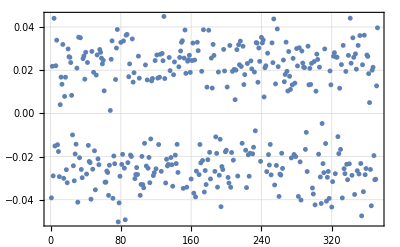

```mathematica
ListPlot[listShim,PlotTheme->"Detailed",PlotMarkers->{Automatic,5}]
```

#### All Phases

```mathematica
DumpGet[StringJoin[dir,"errors2.mx"]]
```

```mathematica
errors2=ConstantArray[{},nphase];

For[mode=1,mode≤ nphase,mode++,
Print["Phase: ", mode];
(*Draw*)
device2=idDraw[typeID="DeltaUndulator",gap,nPeriods,periodL,blockGeo,blockThick,blockGap,magnetizations2,terminations2,mode,subdiv ,{0,0}];
(*Apply Shimming*)
blockIdx=0;
For[j=1,j≤Length[magnetizations2],j++,
For[i =1,i≤nCasseteBl,i++,
blockIdx+=1;
cassetteID=radObjCntStuf[device2][[j]];
radTrfOrnt[radObjCntStuf[cassetteID][[i]],radTrfTrsl[{0,0,listShim[[blockIdx]]}]];
];
];
(*Solve*)
idSolve[device2];
(*Field*)
baxis2=idField[device2,li,lf,lNpts,{0,0},display=0,oneplot=1];
(*Integral*)
outInt2=idFieldInt[device2,li,lf,lstep,baxis2,display=0,oneplot=0];
(*Trajectory*)
Trajetoria2=idTrajectory[device2, eEnergy,r0={0,0,li,0,0,1},lf,lstep,display=0];
(*Phase error*)
phError2=idPhaseError[baxis2,li,lf,lNpts,Trajetoria2,eEnergy];

errors2[[mode]]={baxis2,outInt2[[1,-1]],outInt2[[2,-1]],Trajetoria2,phError2};
];
```

Phase: 1

Phase: 2

Phase: 3

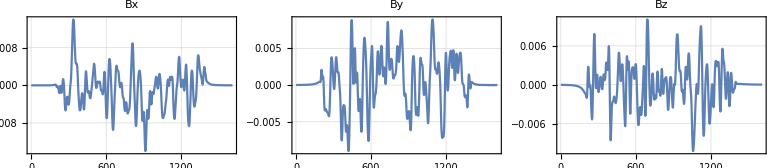

```mathematica
GraphicsRow[{ListLinePlot[errors2[[1,1,All,1]]-errors1[[1,1,All,1]],PlotTheme->"Detailed",PlotLabel->"Bx"],ListLinePlot[errors2[[1,1,All,2]]-errors1[[1,1,All,2]],PlotTheme->"Detailed",PlotLabel->"By"],ListLinePlot[errors2[[1,1,All,3]]-errors1[[1,1,All,3]],PlotTheme->"Detailed",PlotLabel->"Bz"]}]
```

```mathematica
longPos=idBlocksPosition[magnetizations2,terminations2,blockThick,blockGap];
```

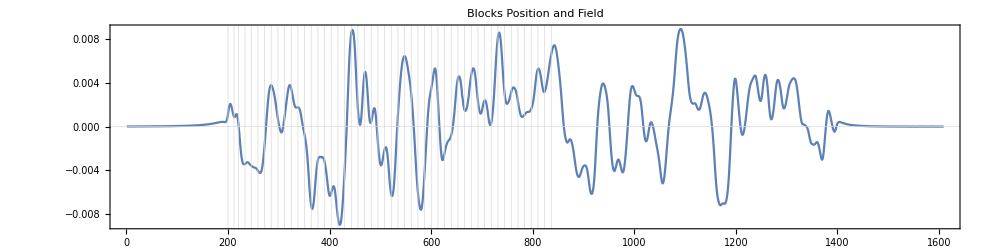

```mathematica
ListLinePlot[errors2[[1,1,All,2]]-errors1[[1,1,All,2]],Frame->True,GridLines->{longPos+oversize,{0}},GridLinesStyle->Directive[LightGray],ImageSize->{1000,200},AspectRatio->2/8,PlotLabel->"Blocks Position and Field"]
```

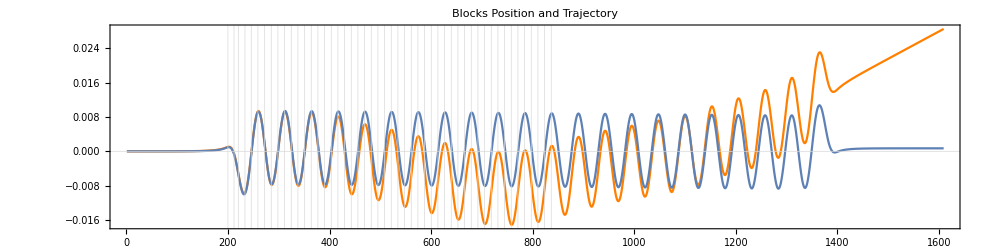

```mathematica
p1=ListLinePlot[errors1[[1,4,All,1]],Frame->True,GridLines->{longPos+oversize,{0}},GridLinesStyle->Directive[LightGray],ImageSize->{1000,200},AspectRatio->2/8,PlotLabel->"Blocks Position and Field"];
p2=ListLinePlot[errors2[[1,4,All,1]],Frame->True,GridLines->{longPos+oversize,{0}},GridLinesStyle->Directive[LightGray],ImageSize->{1000,200},AspectRatio->2/8,PlotLabel->"Blocks Position and Trajectory",PlotStyle->{Orange}];
Show[{p2,p1}]
```

```mathematica
diffT=Table[{li+(i-1)*lstep,errors2[[1,4,i,1]]-errors1[[1,4,i,1]]},{i,1,Length[errors1[[1,4]]]}];

Show[{ListLinePlot[diffT,Frame->True,GridLines->{longPos,{0}},ImageSize->{1000,400},AspectRatio->2/5,PlotLabel->Style["Trajectory Difference from Ideal Undulator (Before Shimming)",Bold,14],FrameLabel->{Style["Longitudinal Axis [mm]",Bold,12],Style["Transversal Axis X [mm]",Bold,12]}],
Graphics[Text[Style["* Vertical Lines represents\nthe Magnets Center",Bold,12],{0.0,Center},{Left,Center}]]
}]
```

-Graphics-

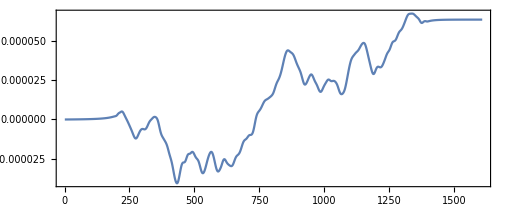

```mathematica
ListLinePlot[Table[(diffT[[i+1,2]]-diffT[[i,2]])/lstep,{i,1,Length[diffT]-1}],AspectRatio->2/5,Frame->True]
```

### > Corrections

```mathematica
shimMatrix=ArrayReshape[listShim,{Length[magnetizations2],nCasseteBl}];
```

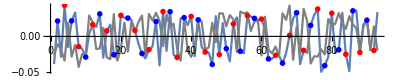

```mathematica
p1=ListLinePlot[shimMatrix[[1]],AspectRatio->1/5];
p4=ListLinePlot[shimMatrix[[3]],PlotStyle->Gray];
p2=ListPlot[Table[{2+4*i,shimMatrix[[1,2+4*i]]},{i,0,Floor[Length[shimMatrix[[1]]]/4]-1}],PlotMarkers->{"OpenMarkers"},PlotLegends->{"UP Mag"},PlotStyle->Blue];
p3=ListPlot[Table[{4+4*i,shimMatrix[[1,4+4*i]]},{i,0,Floor[Length[shimMatrix[[1]]]/4]-1}],PlotMarkers->{"OpenMarkers"},PlotLegends->{"Down Mag"},PlotStyle->Red];
Show[{p1,p4,p2,p3}]
```

#### Shimming

```mathematica
(*(*Push exit down*)
Do[radTrfOrnt[radObjCntStuf[cassetteID][[i]],radTrfTrsl[{0,0,-0.3}]];,{i,{48,52,56}}]        (*magdown*)
Do[radTrfOrnt[radObjCntStuf[cassetteID][[i]],radTrfTrsl[{0,0,0.3}]];,{i,{50,54}}] (*magup*)
Do[radTrfOrnt[radObjCntStuf[cassetteID][[i]],radTrfTrsl[{0,0,-0.2}]];,{i,{84,88,92}}]        (*magdown*)
Do[radTrfOrnt[radObjCntStuf[cassetteID][[i]],radTrfTrsl[{0,0,0.2}]];,{i,{82,86,90}}] (*magup*)
(*Push Center down*)
Do[radTrfOrnt[radObjCntStuf[cassetteID][[i]],radTrfTrsl[{0,0,0.1}]];,{i,{38,42,22,26,30}}]  (*magup*)
Do[radTrfOrnt[radObjCntStuf[cassetteID][[i]],radTrfTrsl[{0,0,-0.1}]];,{i,{40,44,20,24,28}}]  (*magdown*)
(*Push Front up*)
Do[radTrfOrnt[radObjCntStuf[cassetteID][[i]],radTrfTrsl[{0,0,-0.25}]];,{i,{10,14,18}}]  (*magup*)
Do[radTrfOrnt[radObjCntStuf[cassetteID][[i]],radTrfTrsl[{0,0,0.25}]];,{i,{8,12,16}}]  (*magdown*)*)
```

```mathematica
(*Draw*)
device3=idDraw[typeID="DeltaUndulator",gap,nPeriods,periodL,blockGeo,blockThick,blockGap,magnetizations2,terminations2,mode=1,subdiv ,{0,0}];
(*Apply Shimming*)
blockIdx=0;
For[j=1,j≤Length[magnetizations2],j++,
For[i =1,i≤nCasseteBl,i++,
blockIdx+=1;
cassetteID=radObjCntStuf[device3][[j]];
radTrfOrnt[radObjCntStuf[cassetteID][[i]],radTrfTrsl[{0,0,listShim[[blockIdx]]}]];
];
];
cassetteID=radObjCntStuf[device3][[1]]; 
cassetteID2=radObjCntStuf[device3][[2]]; 
cassetteID3=radObjCntStuf[device3][[3]];
cassetteID4=radObjCntStuf[device3][[4]];
```

```mathematica
(*Push exit down*)
Do[radTrfOrnt[radObjCntStuf[cassetteID2][[i]],radTrfTrsl[{0,0,-0.3}]];,{i,{48,52,56}}]        (*magdown*)
Do[radTrfOrnt[radObjCntStuf[cassetteID2][[i]],radTrfTrsl[{0,0,0.3}]];,{i,{50,54}}] (*magup*)
Do[radTrfOrnt[radObjCntStuf[cassetteID2][[i]],radTrfTrsl[{0,0,-0.2}]];,{i,{84,88,92}}]        (*magdown*)
Do[radTrfOrnt[radObjCntStuf[cassetteID2][[i]],radTrfTrsl[{0,0,0.2}]];,{i,{82,86,90}}] (*magup*)
(*Push Center down*)
Do[radTrfOrnt[radObjCntStuf[cassetteID2][[i]],radTrfTrsl[{0,0,0.1}]];,{i,{38,42,22,26,30}}]  (*magup*)
Do[radTrfOrnt[radObjCntStuf[cassetteID2][[i]],radTrfTrsl[{0,0,-0.1}]];,{i,{40,44,20,24,28}}]  (*magdown*)
(*Push Front up*)
Do[radTrfOrnt[radObjCntStuf[cassetteID2][[i]],radTrfTrsl[{0,0,-0.25}]];,{i,{10,14,18}}]  (*magup*)
Do[radTrfOrnt[radObjCntStuf[cassetteID2][[i]],radTrfTrsl[{0,0,0.25}]];,{i,{8,12,16}}]  (*magdown*)

(*Solve*)
idSolve[device3];
(*Trajectory*)
Trajetoria3=idTrajectory[device3, eEnergy,r0={0,0,li,0,0,1},lf,lstep,display=0];

diffT2=Table[{li+(i-1)*lstep,Trajetoria3[[i,1]]-errors1[[1,4,i,1]]},{i,1,Length[errors1[[1,4]]]}];
```

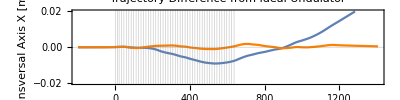

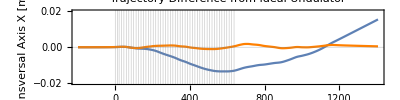

```mathematica
(*Plot*)
Show[ListLinePlot[diffT,PlotLegends->{"Before"},Frame->True,PlotRange->{All,{-0.02,0.02}}],ListLinePlot[diffT2,PlotStyle->Orange,PlotLegends->{"After"}],PlotLabel->Style["Trajectory Difference from Ideal Undulator",Bold,14],FrameLabel->{Style["Longitudinal Axis [mm]",Bold,12],Style["Transversal Axis X [mm]",Bold,12]},GridLines->{longPos,{0}},AspectRatio->2/8]
```

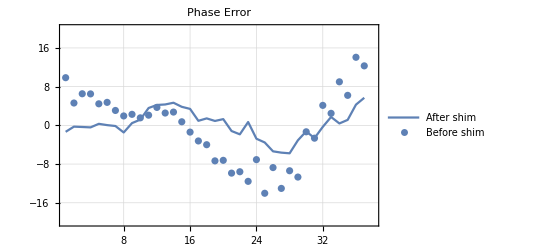

```mathematica
baxis3=idField[device3,li,lf,lNpts,{0,0},display=0,oneplot=1];
(*Phase error*)
phError3=idPhaseError[baxis3,li,lf,lNpts,Trajetoria3,eEnergy];
Show[ListLinePlot[phError3,PlotTheme->"Detailed",PlotLabel-> "Phase Error",PlotLegends->{"After shim"}],ListPlot[phError2,PlotTheme->"Detailed",PlotLegends->{"Before shim"}],PlotRange-> {All,{-20,20}}]
```

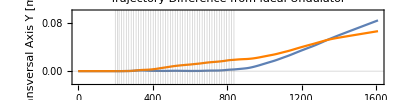

```mathematica
(*Plot*)
j=2;
Show[ListLinePlot[errors2[[1,4,All,j]],PlotLegends->{"Before"},Frame->True,PlotRange->{-0.02,0.1}],ListLinePlot[Trajetoria3[[All,j]],PlotStyle->Orange,PlotLegends->{"After"}],PlotLabel->Style["Trajectory Difference from Ideal Undulator",Bold,14],FrameLabel->{Style["Longitudinal Axis [mm]",Bold,12],Style["Transversal Axis Y [mm]",Bold,12]},GridLines->{longPos+oversize,{0}},AspectRatio->2/8]
```

### > Teste para todas as fases

```mathematica
errors3=ConstantArray[{},nphase];

For[mode=1,mode≤ nphase,mode++,
Print["Phase: ", mode];
(*Draw*)
device3=idDraw[typeID="DeltaUndulator",gap,nPeriods,periodL,blockGeo,blockThick,blockGap,magnetizations2,terminations2,mode,subdiv ,{0,0}];
(*Apply Shimming*)
blockIdx=0;
For[j=1,j≤Length[magnetizations2],j++,
For[i =1,i≤nCasseteBl,i++,
blockIdx+=1;
cassetteID=radObjCntStuf[device3][[j]];
radTrfOrnt[radObjCntStuf[cassetteID][[i]],radTrfTrsl[{0,0,listShim[[blockIdx]]}]];
];
];
cassetteID2=radObjCntStuf[device3][[2]]; (*Por enquanto só no cassete 1*)

(*Push exit down*)
Do[radTrfOrnt[radObjCntStuf[cassetteID2][[i]],radTrfTrsl[{0,0,-0.3}]];,{i,{48,52,56}}];       (*magdown*)
Do[radTrfOrnt[radObjCntStuf[cassetteID2][[i]],radTrfTrsl[{0,0,0.3}]];,{i,{50,54}}]; (*magup*)
Do[radTrfOrnt[radObjCntStuf[cassetteID2][[i]],radTrfTrsl[{0,0,-0.2}]];,{i,{84,88,92}}];        (*magdown*)
Do[radTrfOrnt[radObjCntStuf[cassetteID2][[i]],radTrfTrsl[{0,0,0.2}]];,{i,{82,86,90}}]; (*magup*)
(*Push Center down*)
Do[radTrfOrnt[radObjCntStuf[cassetteID2][[i]],radTrfTrsl[{0,0,0.1}]];,{i,{38,42,22,26,30}}];  (*magup*)
Do[radTrfOrnt[radObjCntStuf[cassetteID2][[i]],radTrfTrsl[{0,0,-0.1}]];,{i,{40,44,20,24,28}}];  (*magdown*)
(*Push Front up*)
Do[radTrfOrnt[radObjCntStuf[cassetteID2][[i]],radTrfTrsl[{0,0,-0.25}]];,{i,{10,14,18}}];  (*magup*)
Do[radTrfOrnt[radObjCntStuf[cassetteID2][[i]],radTrfTrsl[{0,0,0.25}]];,{i,{8,12,16}}];  (*magdown*)

(*Solve*)
idSolve[device3];
(*Field*)
baxis3=idField[device3,li,lf,lNpts,{0,0},display=0,oneplot=1];
(*Integral*)
outInt3=idFieldInt[device3,li,lf,lstep,baxis3,display=0,oneplot=0];
(*Trajectory*)
Trajetoria3=idTrajectory[device3, eEnergy,r0={0,0,li,0,0,1},lf,lstep,display=0];
(*Phase error*)
phError3=idPhaseError[baxis3,li,lf,lNpts,Trajetoria3,eEnergy];

errors3[[mode]]={baxis3,outInt3[[1,-1]],outInt3[[2,-1]],Trajetoria3,phError3};
];
```

Phase: 1

Phase: 2

Phase: 3

```mathematica
dir=NotebookDirectory[];
DumpSave[StringJoin[dir,"errors1.mx"],errors1];
DumpSave[StringJoin[dir,"errors2.mx"],errors2];
DumpSave[StringJoin[dir,"errors3.mx"],errors3];
```

```mathematica
(*errors = {baxis3,outInt3[[1,-1]],outInt3[[2,-1]],Trajetoria3,phError3}*)

For[mode=1,mode≤ nphase,mode++,
Print[Style["=====> Phase ",Bold,13],mode,Style[" (Pol. Hor.)",Bold,13],"\n> Trajetoria Erro de Saída(x,y) [μm]:\n","Perfeito =\t",errors1[[mode,4,-1,1;;2]]*10^3,"\nC/ Erros =\t",errors2[[mode,4,-1,1;;2]]*10^3,"\nShimming =\t",errors3[[mode,4,-1,1;;2]]*10^3];

Print["\n> Erro de Fase RMS [deg]:\n","Perfeito =\t",RootMeanSquare[errors1[[mode,5]]],"\nC/ Erros =\t",RootMeanSquare[errors2[[mode,5]]],"\nShimming =\t",RootMeanSquare[errors3[[mode,5]]]];

Print["\n> First Integral [G.cm]:\n","Perfeito =\t",errors1[[mode,2]],"\nC/ Erros =\t",errors2[[mode,2]],"\nShimming =\t",errors3[[mode,2]]];

Print["\n> Second Integral [kG.cm.b2]:\n","Perfeito =\t",errors1[[mode,3]],"\nC/ Erros =\t",errors2[[mode,3]],"\nShimming =\t",errors3[[mode,3]],"\n"];

]
```

=====> Phase 1 (Pol. Hor.)
> Trajetoria Erro de Saída(x,y) [μm]:
Perfeito =	{0.69712,0.000121713}
C/ Erros =	{16.2305,85.0281}
Shimming =	{1.18599,66.9527}

> Erro de Fase RMS [deg]:
Perfeito =	0.397525
C/ Erros =	6.8131
Shimming =	2.85458

> First Integral [G.cm]:
Perfeito =	{-0.393528,-0.214934,0.00101352}
C/ Erros =	{-1184.37,532.144,0.210937}
Shimming =	{-518.959,-29.7617,0.354371}

> Second Integral [kG.cm.b2]:
Perfeito =	{-0.0456778,0.685261,-0.000510414}
C/ Erros =	{-85.0196,16.0612,-2.32052}
Shimming =	{-67.2796,1.11187,-3.36987}

=====> Phase 2 (Pol. Hor.)
> Trajetoria Erro de Saída(x,y) [μm]:
Perfeito =	{-2.23794,0.687269}
C/ Erros =	{12.6462,83.2944}
Shimming =	{-3.77328,66.7464}

> Erro de Fase RMS [deg]:
Perfeito =	0.675345
C/ Erros =	20.7478
Shimming =	12.5037

> First Integral [G.cm]:
Perfeito =	{-9.20375,0.85571,0.00869014}
C/ Erros =	{-1174.3,530.925,-0.0949102}
Shimming =	{-563.625,-80.2745,0.0490764}

> Second Integral [kG.cm.b2]:
Perfeito =	{-0.750822,-2.09525,0.000376046}
C/ Erros =	{-83.3585,12.4867,-2.36024}
Shimming =	{-67.0798,-3.8207,-3.394}

=====> Phase 3 (Pol. Hor.)
> Trajetoria Erro de Saída(x,y) [μm]:
Perfeito =	{2.91549,4.11186}
C/ Erros =	{16.7432,86.5111}
Shimming =	{-1.10582,71.2144}

> Erro de Fase RMS [deg]:
Perfeito =	0.387256
C/ Erros =	8.18096
Shimming =	3.9881

> First Integral [G.cm]:
Perfeito =	{-51.9992,-0.272699,-0.00467529}
C/ Erros =	{-1223.13,526.263,-0.378259}
Shimming =	{-661.346,-140.948,-0.190321}

> Second Integral [kG.cm.b2]:
Perfeito =	{-4.14106,2.89559,-0.00107871}
C/ Erros =	{-86.5892,16.7551,-2.39441}
Shimming =	{-71.6801,-1.13715,-3.43857}

#### Plot Results

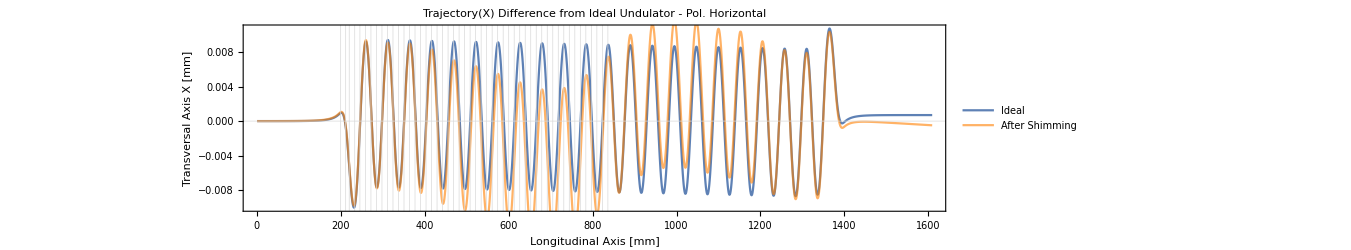

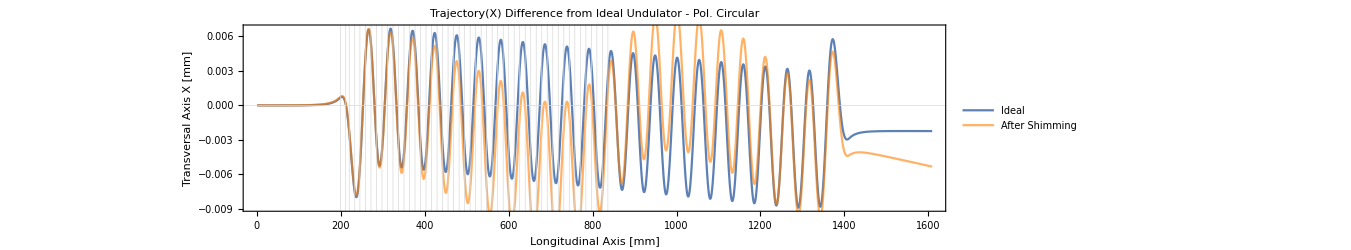

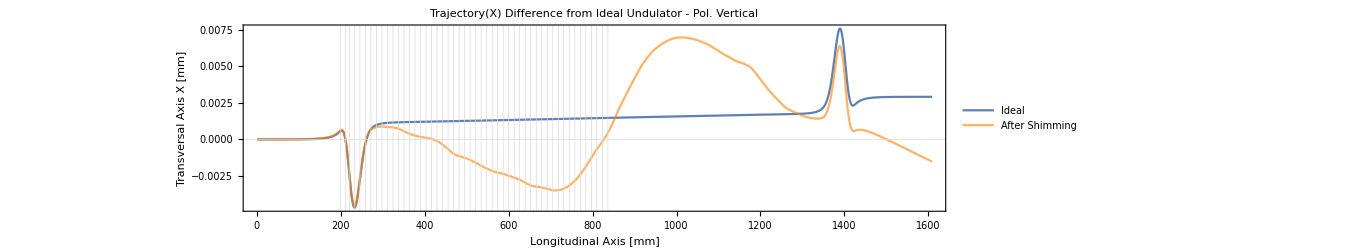

```mathematica
titlePhase={"Horizontal","Circular","Vertical"};
For[mode=1,mode≤ nphase,mode++,
p1=ListLinePlot[errors1[[mode,4,All,1]],Frame->True,GridLines->{longPos+oversize,{0}},GridLinesStyle->Directive[LightGray],ImageSize->{1000,300},AspectRatio->1/4,PlotLabel->Style[StringJoin["Trajectory(X) Difference from Ideal Undulator - Pol. ",titlePhase[[mode]]],Bold,14],PlotLegends->Placed[{"Ideal"},Right],PlotRange->All,FrameLabel->{Style["Longitudinal Axis [mm]",Bold,12],Style["Transversal Axis X [mm]",Bold,12]}];

p2=ListLinePlot[errors3[[mode,4,All,1]],Frame->True,GridLines->{longPos+oversize,{0}},ImageSize->{1000,300},AspectRatio->1/4,PlotStyle->{Opacity[0.6,Orange]},PlotLegends->Placed[{"After Shimming"},Right],PlotRange->All];
Print[Show[{p1,p2}]]
]
```

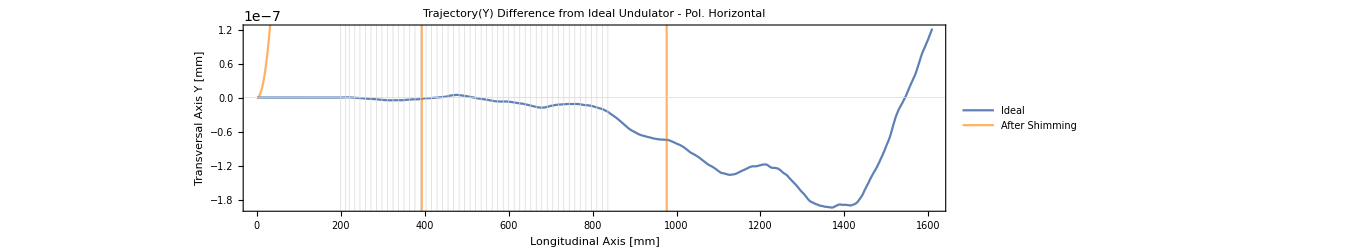

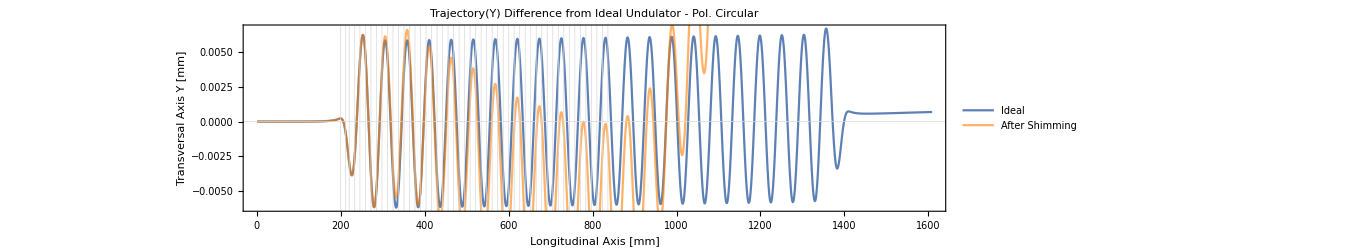

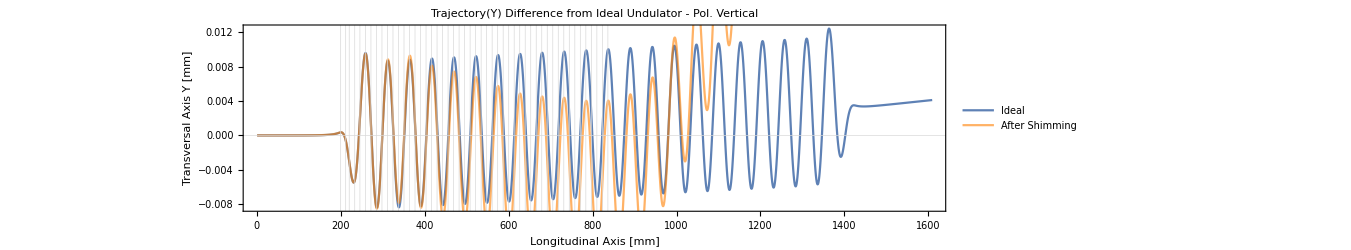

```mathematica
titlePhase={"Horizontal","Circular","Vertical"};
For[mode=1,mode≤ nphase,mode++,
p1=ListLinePlot[errors1[[mode,4,All,2]],Frame->True,GridLines->{longPos+oversize,{0}},GridLinesStyle->Directive[LightGray],ImageSize->{1000,300},AspectRatio->1/4,PlotLabel->Style[StringJoin["Trajectory(Y) Difference from Ideal Undulator - Pol. ",titlePhase[[mode]]],Bold,14],PlotLegends->Placed[{"Ideal"},Right],PlotRange->All,FrameLabel->{Style["Longitudinal Axis [mm]",Bold,12],Style["Transversal Axis Y [mm]",Bold,12]}];

p2=ListLinePlot[errors3[[mode,4,All,2]],Frame->True,GridLines->{longPos+oversize,{0}},ImageSize->{1000,300},AspectRatio->1/4,PlotStyle->{Opacity[0.6,Orange]},PlotLegends->Placed[{"After Shimming"},Right],PlotRange->All];
Print[Show[{p1,p2}]]
]
```

### > Método da Media no Periodo

```mathematica
(*Draw*)
device4=idDraw[typeID="DeltaUndulator",gap,nPeriods,periodL,blockGeo,blockThick,blockGap,magnetizations2,terminations2,mode=1,subdiv ,{0,0}];
(*Apply Shimming*)
blockIdx=0;
For[j=1,j≤Length[magnetizations2],j++,
For[i =1,i≤nCasseteBl,i++,
blockIdx+=1;
cassetteID=radObjCntStuf[device4][[j]];
radTrfOrnt[radObjCntStuf[cassetteID][[i]],radTrfTrsl[{0,0,listShim[[blockIdx]]}]];
];
];
cassetteID=radObjCntStuf[device4][[1]]; 
cassetteID2=radObjCntStuf[device4][[2]]; 
cassetteID3=radObjCntStuf[device4][[3]];
cassetteID4=radObjCntStuf[device4][[4]];
```

```mathematica
Trajetoria4=idTrajectory[device4, eEnergy,r0={0,0,li,0,0,1},lf,lstep=0.5,display=0];

TrajectInside=Trajetoria4[[oversize/0.5+1;;-(oversize/0.5)-1,All]];
```

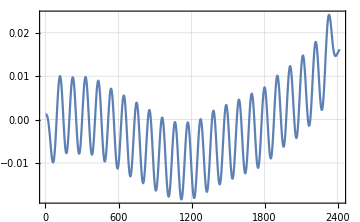
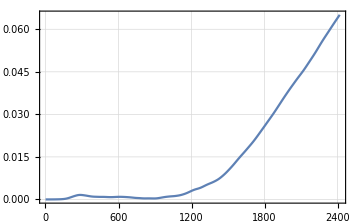

```mathematica
Row[{ListLinePlot[Trajetoria4[[oversize/0.5+1;;-(oversize/0.5)-1,1]],ImageSize->Medium,PlotTheme->"Detailed"],ListLinePlot[Trajetoria4[[oversize/0.5+1;;-(oversize/0.5)-1,2]],ImageSize->Medium,PlotTheme->"Detailed"]},"\t\t"]
```

```mathematica
termLength=3.25*2+9.75*2+8.7+2+3.3+1;
termN=Floor[termLength/0.5];
periodN=Floor[periodL/0.5];
```

```mathematica
meanTraject=ConstantArray[{},nPeriods];
For[i=1,i≤ nPeriods,i++,
meanTraject[[i]]=Mean[TrajectInside[[(i-1)*periodN+1;;i*periodN,All]]]
]
```

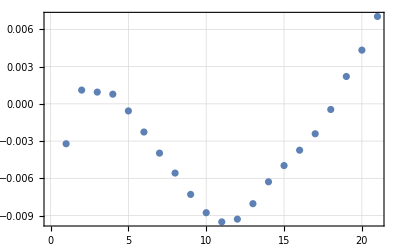

```mathematica
ListPlot[meanTraject[[All,1]],PlotTheme->"Detailed"]
```

Quando utilizamos a média, estamos fazendo uma suavização dos erros da trajetória. Pelo gráfico acima, começaríamos a fazer alguma correção a partir do período 5, mas quando olhamos diretamente para a trajetória, ou melhor, para a diferença com relação à trajetória ideal, vemos que os primeiros blocos a sofrerem shimming são o 8 e o 10, pertencentes  ao primeiro cassete.

### Outros

```mathematica
Show[Graphics3D[radObjDrw[cassetteID],PlotLabel->typeID,BaseStyle->{14,FontFamily->"Times"}],ImageMargins->5,ImageSize->{600,350}]
```

-Graphics3D-

```mathematica
(*===== Generate Errors =====*)
phi=RandomReal[{0,2*Pi},Length[Flatten[magnetization,1]]];
phi=ArrayReshape[phi,{Length[magnetization],Length[magnetization[[1]]]}];

theta=Table[RandomVariate[NormalDistribution[0,(magTheta*Pi/180)/3]],{i,1,Length[Flatten[magnetization,1]]}];
theta=ArrayReshape[theta,{Length[magnetization],Length[magnetization[[1]]]}]; 

If[magError≥1,
dmag=1+Table[RandomVariate[NormalDistribution[0,magAmpError/3]],{i,1,Length[Flatten[magnetization,1]]}];
dmag=ArrayReshape[dmag,{Length[magnetization],Length[magnetization[[1]]]}]; 
,
dmag=ConstantArray[1,{Length[magnetization],Length[magnetization[[1]]]}];
phi=phi*0;
theta=theta*0;
];

(*===== Apply Errors =====*)
For[i=1,i≤ Length[magnetization],i++,
magnetization[[i]]=magnetization[[i]]*dmag[[i]];

For[j=1,j≤ Length[magnetization[[1]]],j++,
If[Mod[j,2]≤0,
magnetization[[i,j]]=RotationMatrix[phi[[i,j]],{0,0,1}].RotationMatrix[theta[[i,j]],{0,1,0}].magnetization[[i,j]];
,
magnetization[[i,j]]=RotationMatrix[phi[[i,j]],{1,0,0}].RotationMatrix[theta[[i,j]],{0,1,0}].magnetization[[i,j]];
];
]
]
```

```mathematica
termMagFront={{{magnAmp,0,0},{0,0,magnAmp},{-magnAmp,0,0},{0,0,-magnAmp}},{{magnAmp,0,0},{0,0,magnAmp},{-magnAmp,0,0},{0,0,-magnAmp}},{{-magnAmp,0,0},{0,0,-magnAmp},{magnAmp,0,0},{0,0,magnAmp}},{{-magnAmp,0,0},{0,0,-magnAmp},{magnAmp,0,0},{0,0,magnAmp}}};


termMagBack={{{0,0,magnAmp},{-magnAmp,0,0},{0,0,-magnAmp},{magnAmp,0,0}},{{0,0,magnAmp},{-magnAmp,0,0},{0,0,-magnAmp},{magnAmp,0,0}},{{0,0,-magnAmp},{magnAmp,0,0},{0,0,magnAmp},{-magnAmp,0,0}},{{0,0,-magnAmp},{magnAmp,0,0},{0,0,magnAmp},{-magnAmp,0,0}}};
```

```mathematica
magError_ :0,magAmpError_ :0.02,magTheta_ :1
```

```mathematica
Dimensions[termMagFront]
```

{4,4,3}

```mathematica
dmag=1+Table[RandomVariate[NormalDistribution[0,magAmpError/3]],{i,1,Length[Flatten[termMagFront,1]]}];
termMagFront=Flatten[termMagFront,1]*dmag;

phi=RandomReal[{0,2*Pi},Length[termMagFront]];
theta=Table[RandomVariate[NormalDistribution[0,(magTheta*Pi/180)/3]],{i,1,Length[termMagFront]}];

For[i=1,i≤ Length[termMagFront],i++,
If[Mod[i,2]≤0,
termMagFront[[i]]=RotationMatrix[phi[[i]],{0,0,1}].RotationMatrix[theta[[i]],{0,1,0}].termMagFront[[i]];
,
termMagFront[[i]]=RotationMatrix[phi[[i]],{1,0,0}].RotationMatrix[theta[[i]],{0,1,0}].termMagFront[[i]];
]
]
termMagFront
```

{{1.37058,-0.000904663,0.000374007},{0.000310501,0.000765349,1.36845},{-1.36472,-0.00487801,-0.00259667},{-0.00290713,0.000809738,-1.36987},{1.36659,0.00520718,0.000437019},{0.0042824,0.00531782,1.37065},{-1.37272,0.0019943,-0.000240814},{0.000022185,-0.0000115138,-1.36215},{-1.37299,-0.00257421,-0.000548732},{-0.00032819,0.00358228,-1.36889},{1.36845,0.0000284945,-0.000106214},{0.00171994,0.00371986,1.37194},{-1.37099,-0.00368792,0.00541022},{0.000119735,0.000278897,-1.36874},{1.37347,0.00435206,0.00508809},{-0.000627854,-0.00308164,1.37269}}